eqn A2 in Martin & Lenormand 2006 Evol shows that when the resident is at the optimum (xi=0) the selective effects of new mutations is distributed as a negative gamma

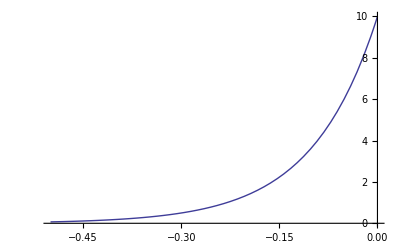

```mathematica
f[s_]:=PDF[GammaDistribution[m/2,λ],-s]
Plot[f[s]/.λ->-2sbar/m/.m->2/.sbar->-0.1,{s,-1/2,0},PlotRange->All]
```

where m is the number of dimensions, λ scales the mean fitness effect -s̄ =m λ / 2, and s is the selection coefficient of the mutation.

To translate to our parameters (in 2D), the mean selective effect of a new mutation from the origin is

```mathematica
Expectation[Log[Exp[-(√(z1^2+z2^2))^2/2]],{z1\[Distributed]NormalDistribution[0,σ],z2\[Distributed]NormalDistribution[0,σ]}]
```

-σ^2

where σ is the SD in the mutational distribution.

Thus in our case λ = 2 σ^2/ 2 = σ^2.

Right, so now we have the rate of mutation to fitness effect s, which is u f[s], where u is the mutation rate. At mutation selection balance we therefore expect to that a mutant with selection coefficient -s will have frequency - u f[s] / s, given s is large enough (-s > 1/Ne, where Ne is the effective population size)

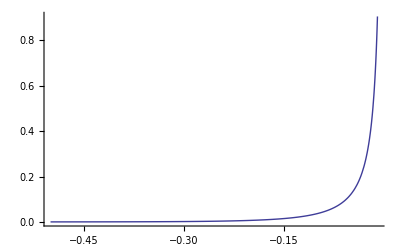

```mathematica
Plot[-u f[s]/s/.λ->-2sbar/m/.m->2/.sbar->-0.1/.u->10^-3,{s,-1/2,-1/100},PlotRange->All]
```

note that this only works if we think of the selective classes of mutants, in [s, s+ds]. Each mutant is unique and is not replaced by mutation (ie there is no mutation selection balance for any particular mutation).

If we instead just look at the expected number of mutations of each selective type produced anew each generation we have

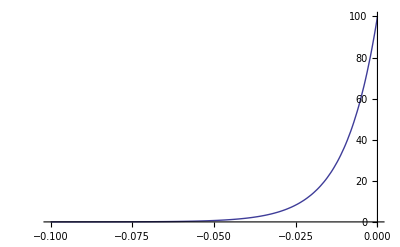

```mathematica
Plot[f[s]/.λ->σ^2/.m->2/.n->10^3/.σ->0.1/.u->10^-4/.B->2,{s,-0.1,0},PlotRange->{0,All}]
```

where B is the number of offspring per capita.